# Review on multidimensional statistics

By Manuel Diaz, NTU, 2013.06.06

Based on B.Flury, A fisrt course in Multivariable Statistics

```mathematica
Quit[];
```

## Generate Random Data

```mathematica
x = Table[RandomInteger[{0,20}],{100}]
```

{7,11,0,3,1,7,0,7,17,3,2,14,7,14,11,18,11,19,8,6,19,13,19,17,12,1,10,12,1,17,5,9,13,12,3,11,3,3,0,9,12,6,4,1,20,9,6,17,7,0,0,14,1,18,18,5,18,11,15,2,13,16,11,2,11,4,4,7,20,11,12,3,5,3,4,20,17,20,18,16,15,11,2,20,10,9,5,16,3,6,12,19,12,10,10,16,14,9,18,5}

```mathematica
Sortx = Sort[Tally[x]];
```

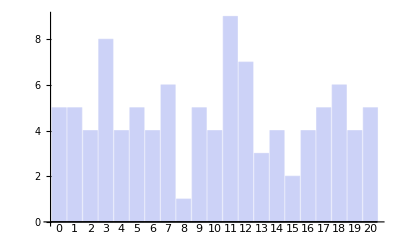

```mathematica
BarChart[Sortx[[All,2]],ChartLabels->Sortx[[All,1]]]
```

```mathematica
xz = Table[RandomInteger[{0,20}],{10},{10}];
xz //TableForm
```

11 | 2 | 0 | 3 | 17 | 11 | 17 | 11 | 13 | 8
6 | 11 | 7 | 13 | 12 | 15 | 13 | 5 | 1 | 7
17 | 15 | 7 | 13 | 20 | 16 | 14 | 2 | 18 | 15
4 | 20 | 13 | 2 | 11 | 13 | 0 | 0 | 2 | 4
6 | 4 | 5 | 14 | 10 | 16 | 1 | 14 | 8 | 3
4 | 4 | 4 | 0 | 1 | 11 | 9 | 13 | 7 | 4
12 | 2 | 6 | 9 | 5 | 20 | 8 | 8 | 6 | 10
11 | 2 | 20 | 5 | 7 | 9 | 16 | 15 | 5 | 12
11 | 4 | 13 | 5 | 18 | 5 | 9 | 3 | 11 | 20
12 | 8 | 3 | 9 | 18 | 1 | 17 | 7 | 7 | 12

## 1D Gauss Statistics,

```mathematica
μ=Mean[x]; (* Mean values *)
σ=StandardDeviation[x]; (* Standar deviation *)
```

```mathematica
p[x_]:= 1/(√(2 π σ^2))Exp[-1/2((x-μ)/σ)^2]
```

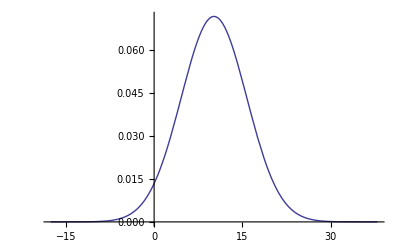

```mathematica
Plot[p[x],{x,μ-5 σ,μ+5 σ}]
```

```mathematica
MomentGeneratingFunction
```

## 2D Gaussian Statistics,

### Isotropic

```mathematica
μ = Mean [Flatten[xz]];
σ = StandardDeviation[Flatten[xz]];
```

```mathematica
1/(√(2 π σ^2))Exp[-1/2((x-μ)/σ)^2] 1/(√(2 π σ^2))Exp[-1/2((y-μ)/σ)^2]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)-(y-μ)^2/(2 σ^2)))/(2 π σ^2)

```mathematica
p[x_,y_]:= (ⅇ^(-(x-μ)^2/(2 σ^2)-(y-μ)^2/(2 σ^2)))/(2 π σ^2)
```

```mathematica
Plot3D[p[x,y],{x,μ-3σ,μ+3σ},{y,μ-3σ,μ+3σ}]
```

-Graphics3D-

### Anisotropic model

in x direction

```mathematica
Subscript[μ, 1] = Mean[xz];
Subscript[σ, 1] = StandardDeviation[xz];
```

```mathematica
Subscript[μ, 1]
```

{47/5,36/5,39/5,73/10,119/10,117/10,52/5,39/5,39/5,19/2}

```mathematica
Subscript[σ, 1]
```

{(√(802/5))/3,√(586/15),(28 √(2/5))/3,(√(2261/10))/3,√(401/10),(√(2861/10))/3,√(574/15),(2 √(317/5))/3,(4 √(73/5))/3,23/(3 √2)}

in y direction

```mathematica
Subscript[μ, 2]=Mean[Transpose[xz]];
Subscript[σ, 2]=StandardDeviation[Transpose[xz]];
```

extra parameter

```mathematica
ρ = 0.5;
```

```mathematica
p[x_,y_] := 1/(2 π Subscript[σ, 1] Subscript[σ, 2](1-ρ^2))Exp[-1/(2(1-ρ^2))(((x-Subscript[μ, 1])/Subscript[σ, 1])^2-2 ρ ((x-Subscript[μ, 1])(y-Subscript[μ, 2]))/(Subscript[σ, 1] Subscript[σ, 2])+((y-Subscript[μ, 2])/Subscript[σ, 2])^2)]
```

```mathematica
Plot3D[p[x,y],{x,Subscript[μ, 1]-3 Subscript[σ, 1],Subscript[μ, 1]+3 Subscript[σ, 1]},{y,Subscript[μ, 2]-3 Subscript[σ, 2],Subscript[μ, 2]+3 Subscript[σ, 2]}]
```

Plot3D::plln: Limiting value {47/5 - √802/5, 36/5 - √1758/5, 39/5 - 28\ √2/5, 73/10 - √2261/10, 119/10 - 3\ √401/10, 117/10 - √2861/10, 52/5 - √1722/5, 39/5 - 2\ √317/5, 39/5 - 4\ √73/5, 19/2 - 23/√2} in {x, μ_1 - 3\ σ_1, μ_1 + 3\ σ_1} is not a machine-sized real number.

Plot3D[p[x,y],{x,μ_1-3 σ_1,μ_1+3 σ_1},{y,μ_2-3 σ_2,μ_2+3 σ_2}]